# Лабораторная работа №4

## по курсу "Системы аналитических вычислений" студент: Ляшун Д. С.

## Варианты:

```mathematica
tasks = {
	Sin[2*x^3]^2/x^3
	, (x^2 - 4)*Sin[(Pi*(x^2))/6] / (x^2 - 1)
	, Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x)
	, 1/2 * Log[Sqrt[x^2 + 1] / Sqrt[x^2 - 1]] - 15*x^2
	, (x^3 - x^2 - x + 1)^(1/3) / Tan[x]
              , 2*Log[(x - 1) / x] + 1
       , Log[x - 1] / (x - 1)^2
}
```

{(Sin[2 x^3]^2)/x^3,((-4+x^2) Sin[(π x^2)/6])/(-1+x^2),(√Abs[-10 x+2 x^2+3 x^3])/(4 x),-15 x^2+1/2 Log[(√(1+x^2))/(√(-1+x^2))],(1-x-x^2+x^3)^(1/3) Cot[x],1+2 Log[(-1+x)/x],Log[-1+x]/(-1+x)^2}

```mathematica
getVariantForNumber[number_, variationsQuo_]:=(
	Module[{t},t = Mod[number , variationsQuo]; If[t ≠ 0
				, t
				, variationsQuo
			]
	] )

yourNumber = 13  (*сюда вбить ваш номер по списку в рейтинге *)
numberOfYourTask = getVariantForNumber[yourNumber, Length[tasks]]
Print["Номер вашего задания: ", numberOfYourTask]
f[y_] := tasks[[numberOfYourTask]]/.x->y;
f[x]//TraditionalForm
```

13

6

Номер вашего задания: 6

2 log((x-1)/x)+1

## 1. График функции

```mathematica
Plot[
	f[x]
	, {x, -10, 10}
    ]
```

-Graphics-

## 2. Область определения

```mathematica
g1[y_] := (x-1)/x  /. x->y;
g2[y_] := x /. x->y;
domain  := Reduce[g1[x]>0, x]
"D(y): "   domain
```

D(y):  (x<0||x>1)

## 3. Является ли функция чётной или нечётной, является ли периодической

### Чётность

```mathematica
res1 = f[x] == f[-x] //TautologyQ
res2 = f[x] + f[-x] == 0 //TautologyQ
If[res1, "Функция четная", Null]
If[res2, "Функция нечетная",Null]
If[Not[res1||res2], "y(x)-y(-x) ≠ 0 и y(x)+y(-x) ≠ 0, поэтому функция не является ни чётной, ни нёчетной", Null]
```

y(x)-y(-x) ≠ 0 и y(x)+y(-x) ≠ 0, поэтому функция не является ни чётной, ни нёчетной

### Периодичность

```mathematica
Print["T = " , FunctionPeriod[f[x], x]]
```

T = 0

Поскольку уравнение имеет решение только при T = 0, получаем, что функция не является периодической.

## 4. Точки пересечения графика с осями координат

### Пересечение с осью OX

```mathematica
sols = Solve[f[x]==0, x]
points = {x, 0}/.sols
p1 = Plot[f[x], {x, -10, 10}];
p2 = ListPlot[points, PlotStyle->{Red, PointSize[Large ]}];
Show[{p1, p2}]
```

-Graphics-

### Пересечение с осью OY

```mathematica
answer = f[0]
```

Power::infy: Infinite expression 1/0 encountered.

∞

При x = 0 функция не определена.

## 5. Промежутки знакопостоянства

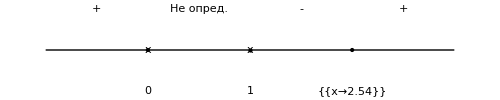

```mathematica
dist = 0.15
size = 500
Show[
   Graphics[Line[{{-1, 0}, {3, 0}}], ImageSize -> size],
   Graphics[Text["0", {0, -dist}], ImageSize -> size],
 Graphics[Text["1", {1, -dist}] , ImageSize -> size],
 Graphics[Text[N[sols, 3], {2, -dist}],  ImageSize -> size],
 Graphics[Point[{0, 0}, VertexColors->Red], ImageSize -> size],
 Graphics[Text["x", {0,0}],  ImageSize -> size],
 Graphics[Text["x", {1,0}], ImageSize -> size],
 Graphics[Point[{1, 0}, VertexColors->Red], ImageSize -> size],
 Graphics[Point[{2, 0}, VertexColors->Red], ImageSize -> size],
 Graphics[Text["+", {-0.5, dist}],ImageSize -> size],
 Graphics[Text["Не опред.", {0.5, dist}],ImageSize -> size],
 Graphics[Text["-", {1.5, dist}],ImageSize -> size],
 Graphics[Text["+", {2.5, dist}],ImageSize -> size]
]
```

## 6. Точки экстремума и значения в этих точках

```mathematica
x = .
df := D[f[x], x]
Plot[df /. x -> z, {z, -10, 10}, Exclusions -> {0, 1}]
solsExpr = Solve[ df==0, x]
If[Length[solsExpr] ≠ 0, Print["Точки экстремума:", solsExpr],Print["Точек экстремума нет."]]
```

-Graphics-

Точек экстремума нет.

## 7. Промежутки возрастания и убывания

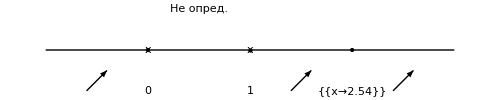

```mathematica
width = 0.1
Show[
   Graphics[Line[{{-1, 0}, {3, 0}}], ImageSize -> size],
   Graphics[Text["0", {0, -dist}], ImageSize -> size],
 Graphics[Text["1", {1, -dist}] , ImageSize -> size],
 Graphics[Text[N[sols, 3], {2, -dist}],  ImageSize -> size],
 Graphics[Point[{0, 0}, VertexColors->Red], ImageSize -> size],
 Graphics[Text["x", {0,0}],  ImageSize -> size],
 Graphics[Text["x", {1,0}], ImageSize -> size],
 Graphics[Point[{1, 0}, VertexColors->Red], ImageSize -> size],
 Graphics[Point[{2, 0}, VertexColors->Red], ImageSize -> size],
 Graphics[Text["Не опред.", {0.5, dist}],ImageSize -> size],
 Graphics[Arrow[{{1.5-width, -dist*1}, {1.5+width, -dist*0.5}}],ImageSize -> size],
 Graphics[Arrow[{{2.5-width, -dist*1}, {2.5+width, -dist*0.5}}],ImageSize -> size],
 Graphics[Arrow[{{-0.5-width, -dist*1}, {-0.5+width, -dist*0.5}}],ImageSize -> size]
]
```

## 8. Непрерывность. Наличие точек разрыва и их классификация

```mathematica
Print["lim [x → 0 - 0] f(x) = ", Limit[f[x], x -> 0, Direction -> "FromAbove"]]
Print["lim [x → 0 + 0] f(x) = ", Limit[f[x], x -> 0, Direction -> "FromBelow"]]
Print["lim [x → 1 - 0] f(x) = ", Limit[f[x], x -> 1, Direction -> "FromAbove"]]
Print["lim [x → 1 + 0] f(x) = ", Limit[f[x], x -> 1, Direction -> "FromBelow"]]
```

lim [x → 0 - 0] f(x) = ∞

lim [x → 0 + 0] f(x) = ∞

lim [x → 1 - 0] f(x) = -∞

lim [x → 1 + 0] f(x) = -∞

Получаем разрывы второго рода в точках x = 0  и  x = 1.

## 9. Асимптоты

```mathematica
Print["lim [x → +∞] f(x) = ", Limit[f[x], x -> +∞]]
Print["lim [x → -∞] f(x) = ", Limit[f[x], x -> -∞]]
```

lim [x → +∞] f(x) = 1

lim [x → -∞] f(x) = 1

Имеем асимптоту y = 1, а также вертикальные асимптоты в точках разрыва x = 1  и  x= 0.

## 10. График функции с асимптотами

```mathematica
Show[
    Plot[f[x], {x, -10, 10}],
  Plot[v = 1, {x, -10, 10}, PlotStyle -> {Red}],
    Graphics[{Dashing[{.05}], Line[{{0, -10}, {0, 10}}]}],
    Graphics[{Dashing[{.05}], Line[{{1, -10}, {1, 10}}]}]
]
```

-Graphics-